# Homework 4

Name: Adel

ID: 201801454

## Problem 1

```mathematica
Clear["Global`*"]
```

a)

```mathematica
sol =DSolve[{T'[t]==-r*(T[t]-a),T[0]==b},T[t],t];
T=T[t]/.sol
```

{ⅇ^(-r t) (-a+b+a ⅇ^(r t))}

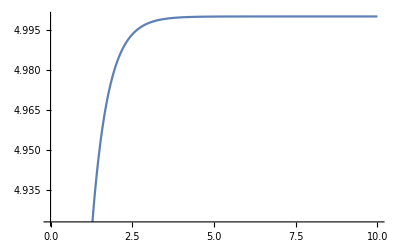

```mathematica
Tplot[r_,a_,b_,t_]:= ⅇ^(-r t) (-a+b+a ⅇ^(r t));
Plot[Tplot[2,5,4,t],{t,0,10}]
```

```mathematica
b
```

b

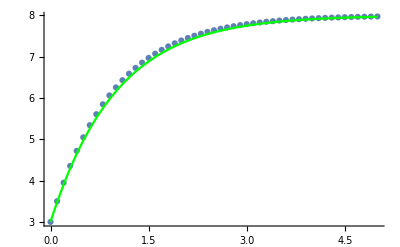

```mathematica
Texact[r_,a_,t0_,t_]:= ⅇ^(-r t) (-a+t0+a ⅇ^(r t)) (* Exact solution *)

(* define our variables *)
a =8.0;r=1;  dt = 0.1; ts = 0.0;tf = 5; T0= 3;
tList = Range[ts,tf,dt];
lt = Length[tList];
Tl = Table[0,{i,lt}];
Tl[[1]] =T0 ;
u1 = 1- dt*r;
u2=dt*r*a;


Do[Tl[[i]] = u1 Tl[[i-1]]+u2,{i,2,lt}];
Tlplot = Table[{tList[[i]],Tl[[i]]},{i,lt}];

(* Results *)
fi1= ListPlot[Tlplot]; 
fi2 =Plot[Tplot[r,a,T0,t],{t,ts,tf},PlotStyle->Green];
Show[fi1,fi2,PlotRange->All]
```

c)

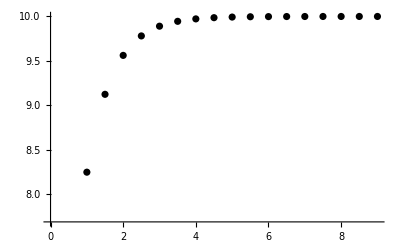
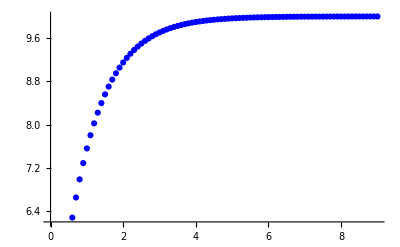
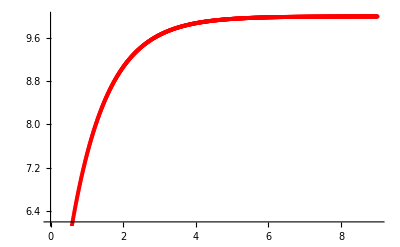

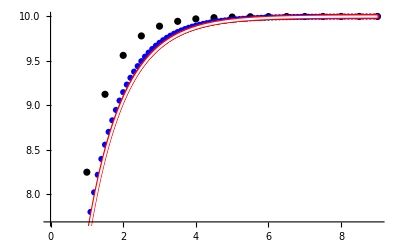

```mathematica
Tnew[r_,a_,t0_,t_]:= ⅇ^(-r t) (-a+t0+a ⅇ^(r t)) 
a =10.0;r=1.0;  ts = 0.0;tf= 9; T0= 3;
sdt = {0.5,0.1,0.01}; 

Plots={1,2,3};
colors= {Black,Blue,Red};


j=1;
Do[ 

tList = Range[ts,tf,dt];
lt = Length[tList];
Tl = Table[0,{i,lt}];
Tl[[1]] =T0 ;
u1 = 1- dt*r;
u2=dt*r*a;


Do[Tl[[i]] = u1 Tl[[i-1]]+u2,{i,2,lt}];
Tlplot = Table[{tList[[i]],Tl[[i]]},{i,lt}];

(* Results *)
Plots[[j]]=Show[ListPlot[Tlplot,PlotStyle->{Dotted,colors[[j]]}]];j=j+1;
,{dt,sdt}];
Plots
Show[Plots,Plot[Tnew[r,a,T0,t],{t,ts,tf},PlotStyle->White]]
```

```mathematica
(* we see how making dt small approches the true value red ---> white*)
```

## Problem 2

```mathematica
Clear[τ,nl,dt]
```

```mathematica
(*Eulers formula meant 
nl[[j]]=nl[[j-1]](1.0-dt/τ)

then we can see 
(*nl[[t]]=*)*)
Limit[n0*(1.0-dt/τ)^(t/dt),dt->0]
```

ⅇ^(-(1. t)/τ) n0

```mathematica
(*which is the exact formaula
the euler formuala above will give as this standard limit*)
```

## Problem 3

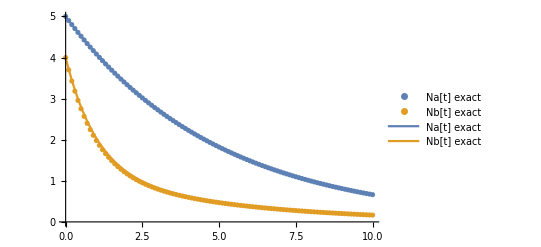

```mathematica
(*exact solution as function of m *)
τb=1 ;
τa=m τb;
eqs={na'[t]==-na[t]/τa,nb'[t]==na[t]/τa+(-nb[t])/τb};
{sol}= {na[t],nb[t]}/.DSolve[{eqs,na[0]==5,nb[0]==4},{na[t],nb[t]},t];
(*Solving eq for general m*)
exactNa[t_,m_]=sol[[1]];
exactNb[t_,m_]=sol[[2]];

(*For the numerical Solution*)
n0a=5;
n0b=4;
τa=5;τb=1;
ts=0;tf=10;
dt=0.1;
tl=Range[ts,tf,dt];
ll=Length[tl];
nla=0tl; nlb=0 tl;
nla[[1]]=n0a;
nlb[[1]]=n0b;
step1 = 1- dt/τa;
step2=1-dt/τb;
Do[{nla[[i]] = step1 *nla[[i-1]],nlb[[i]] = step2  nlb[[i-1]]+(dt/τa)nla[[i-1]]},{i,2,ll}];(* Euler method *)
(*comparing*)
ListNa = Table[{tl[[i]],nla[[i]]},{i,ll}];
ListNb= Table[{tl[[i]],nlb[[i]]},{i,ll}];
fig1=ListPlot[{ListNa,ListNb},PlotLegends->{"Na[t] exact","Nb[t] exact"}];
fig2=Plot[{exactNa[t,5],exactNb[t,5]},{t,ts,tf},PlotLegends->{"Na[t] exact","Nb[t] exact"}];
Show[{fig1,fig2}]
Manipulate[Plot[{exactNa[t,m],exactNb[t,m]},{t,0,10},PlotLegends->{"Na[t] exact","Nb[t] exact"},PlotStyle->{Blue,Red} ],{m,1.1,6}]
Manipulate[Plot[{exactNa[t,m],exactNb[t,m]},{t,0,10},PlotLegends->{"Na[t] exact","Nb[t] exact"},PlotStyle->{Blue,Red}],{m,0.1,0.9}]
```